# EQLab package quick guide.

## Useful Info

1) Some definitions:

1.1) USER         →    one of us, someone who runs this package.

1.2) predictor → an expert, a person whose behaviour/belief we try to model

1.3) question  →  a  basic  ‘unit’ in an experiment, indexed by ‘i’.  Asking a question (fixed i) is  step that involves producing:
	a) forecasts  p_ij for each predictor ( for all values of   j )
	b) a measurement m_i (like tossing a die)
	c) resolutions v_ij for each predictor  ( for all values of   j ) 
	d) outcome q_i ( this reflects the resolution of the majority of predictors  )
	e) surprisals s_ij for each predictor  ( for all values of   j ) 
	f)  rewards r_ij  for each predictor  ( for all values of   j )  
	A question is stored in EQLab as a List :  question_i={p_i,m_i,v_i,q,s_i,r_i};  Where bold letters are each a List
	
1.4) Experiment → a set of questions asked in sequence (stored as a List of questions)

2)Some variable definitions:

2.1) npredictors →  number of  predictors  (cannot be modified after loading EQLab )
         nquestions →  number of  questions for each experiment (can be modified in between experiments)

2.2) npredictorsUSER →   number of  predictors, to be defined by user before  loading EQLab. (have no effect after loading)

## Steps to prepare simulations

Set user parameter values

```mathematica
npredictorsUSER=5;
```

Load package

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
<<EQLab`
```

Define functions needed for experiment. Needs the follow the prototypes below:

UserPredict[exp_ , newquestion_]       →  Function should return a List of numbers (forecasts) of size ‘npredictors’ ;    ‘exp’  and ‘newquestion’  are  as defined in EQLab  it is useful if predictors update their forecast based on previous questions and/or current measurement .

TR - set random number seed to try to compare with what i had before

```mathematica
SeedRandom[104]
```

RandomGeneratorState[…]

```mathematica
(*set initial forecast*)
setforecastinit[]:=(forecastinit=Table[Random[],{i,1,npredictors}];);
```

TR - changed these to match my dice game.

```mathematica
forecastinit={1/3,5/6,2/3,1/6,1/2}//N;
(*random numbers M to model how each predictor 'reacts' for previous measurements*)
(*smaller M means more reactive*)
setreactioninit[]:=(reactivity=Table[RandomInteger[{1,20}],{i,1,npredictors}];)
reactivity={1,100,1,100};
```

TR - Updated prediction module to not have the forecasts modified

```mathematica
UserPredict[exp_,newquestion_]:=Module[
{REACTIVITY=reactivity,M,ipredictor,n=(exp//Length),ρnew,ρ,m,RHOnew={}},


For[ipredictor=1,ipredictor≤npredictors,ipredictor++,
If[n==0,
ρnew=forecastinit[[ipredictor]],
ρnew=forecastinit[[ipredictor]];
];
AppendTo[RHOnew,ρnew];];
RHOnew]
```

UserMeasure[] 	      →    Function should return either    +1 or -1.  (yes or no, like the toss of a die.)

TR - Changed prob to 1/3

```mathematica
prob=1/3;
UserMeasure[]:=(Random[]//Which[#<prob,1,True,-1]&);
```

UserResolve[exp_ , newquestion_]  	      →    Function should use the List  ‘newquestion[[2]]’ ( forecasts), and  return a List of numbers (resolutions) of the same size.  Arguments are   an experiment  and a question  as defined in EQLab. The variable ‘exp’ is useful only when modeling predictors that use knowledge from previous  questions in the experiment. Even If ‘exp’ is not used, the function must adhere to the  prototype.

```mathematica
UserResolve[experiment_,question_]:=UserResolve[question];
UserResolve[question_]:=Table[Random[]//Which[#<0.5,-question[[2]],True,question[[2]]]&,{i,1,question[[1]]//Length}]
```

## Perform Experiments

#### Results of experiments are stored in the List called ‘EXPERIMENT’

```mathematica
EXPERIMENT
```

{}

#### By default, EQLab loads some predefined functions, So you can run an experiment.

```mathematica
RunExperiment[]
```

#### Now EXPERIMENT has one element (one experiment)

```mathematica
EXPERIMENT//Length
```

1

#### One can run another experiment, and check the size of EXPERIMENT again

```mathematica
RunExperiment[]
EXPERIMENT//Length
```

2

#### See contents of experiment 1

```mathematica
EXPERIMENT[[1]]//MatrixForm
```

({0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,-1,-1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.62874,-0.0633886,0.994881,0.0349973,0.643962}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,-1,-1,1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.377244,-0.0380332,0.596929,0.0209984,0.386377}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,-1,1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.377244,-0.0380332,0.596929,0.0209984,0.386377}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,-1,-1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.62874,-0.0633886,0.994881,0.0349973,0.643962}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,-1,-1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.62874,-0.0633886,0.994881,0.0349973,0.643962}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,-1,-1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.62874,-0.0633886,0.994881,0.0349973,0.643962}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.348407,0.601868,-0.216872,0.583676,0.336923}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,1,-1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.377244,-0.0380332,0.596929,0.0209984,0.386377}
{0.537861,0.835713,0.201294,0.809694,0.527229} | 1 | {1,1,-1,1,1} | 1 | {0.620155,0.17947,1.60299,0.211099,0.64012} | {0.209044,0.361121,-0.130123,0.350206,0.202154}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,-1,-1,-1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.62874,-0.0633886,0.994881,0.0349973,0.643962}
{0.537861,0.835713,0.201294,0.809694,0.527229} | -1 | {-1,1,-1,-1,-1} | -1 | {0.77189,1.80614,0.224763,1.65912,0.749144} | {0.377244,-0.0380332,0.596929,0.0209984,0.386377})

#### Use ShowPlots[] to see results for the lastest experiment (plots are stored in the ‘SUPERARRAY‘ called ‘PLOTS’. )

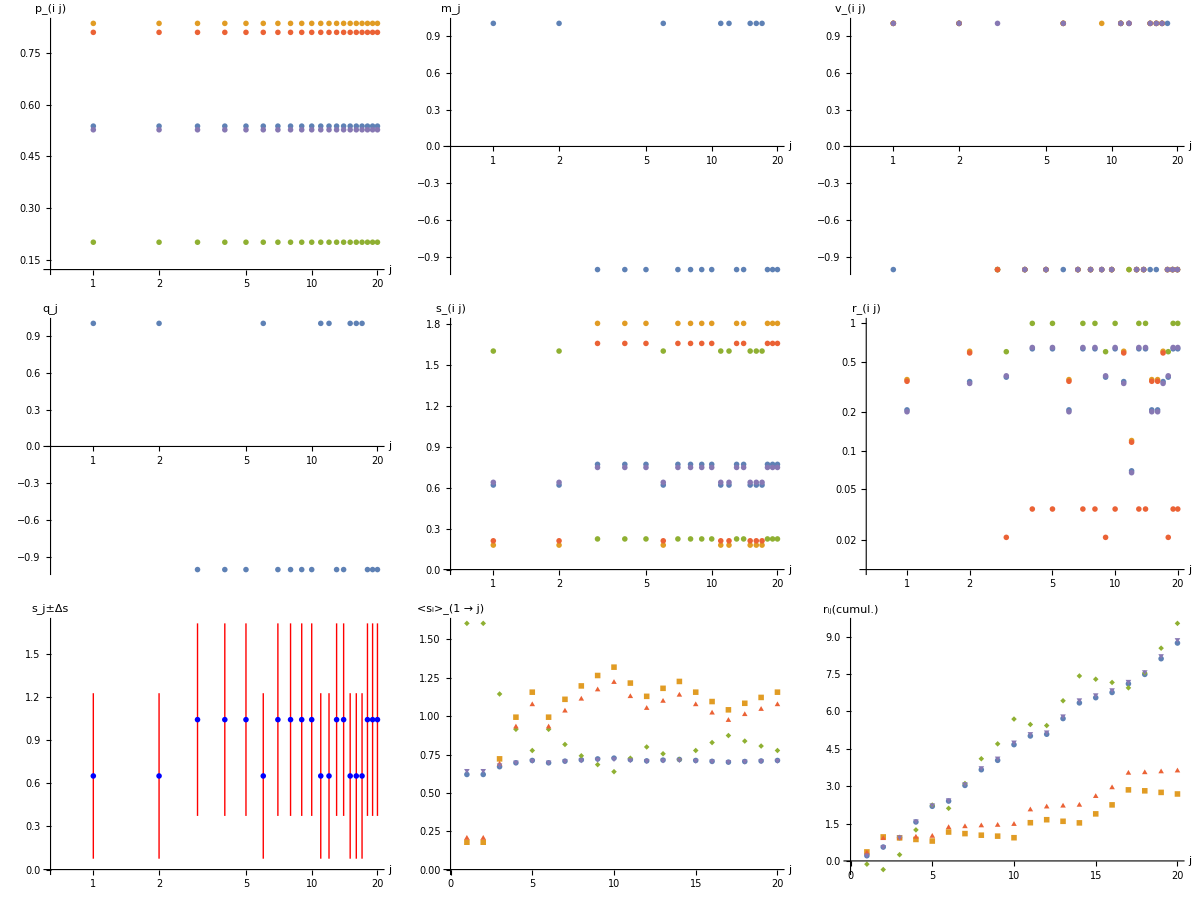

```mathematica
ShowPlots[]
```

#### Use ShowPlots[i] to see results for the ith experiment (plots are stored in the ‘SUPERARRAY‘ called ‘PLOTS’. )

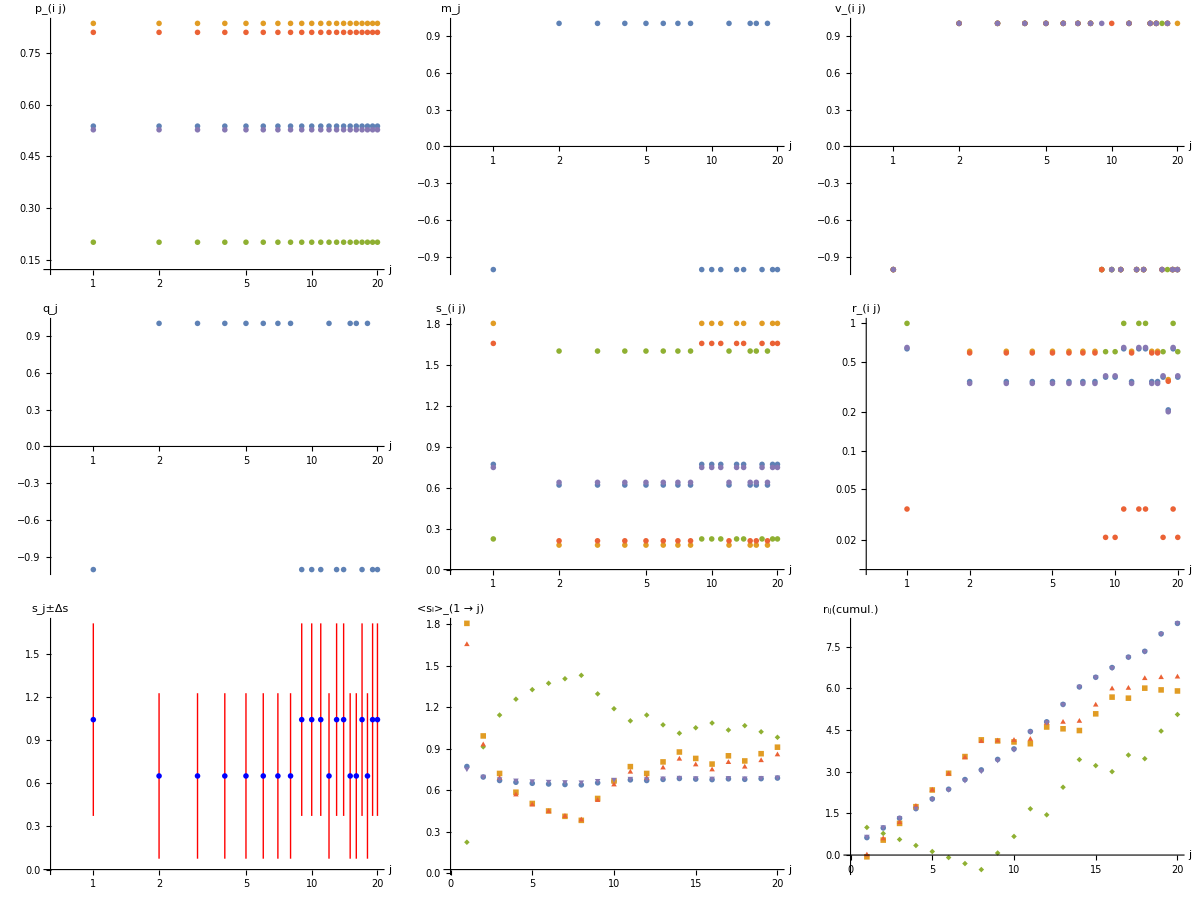

```mathematica
ShowPlots[1]
```

#### Experiments 1 and 2 where done with default functions and default values for ‘nquestions’. To use the custom functions defined above, one needs to load them with ‘SetUserFunctions[]’

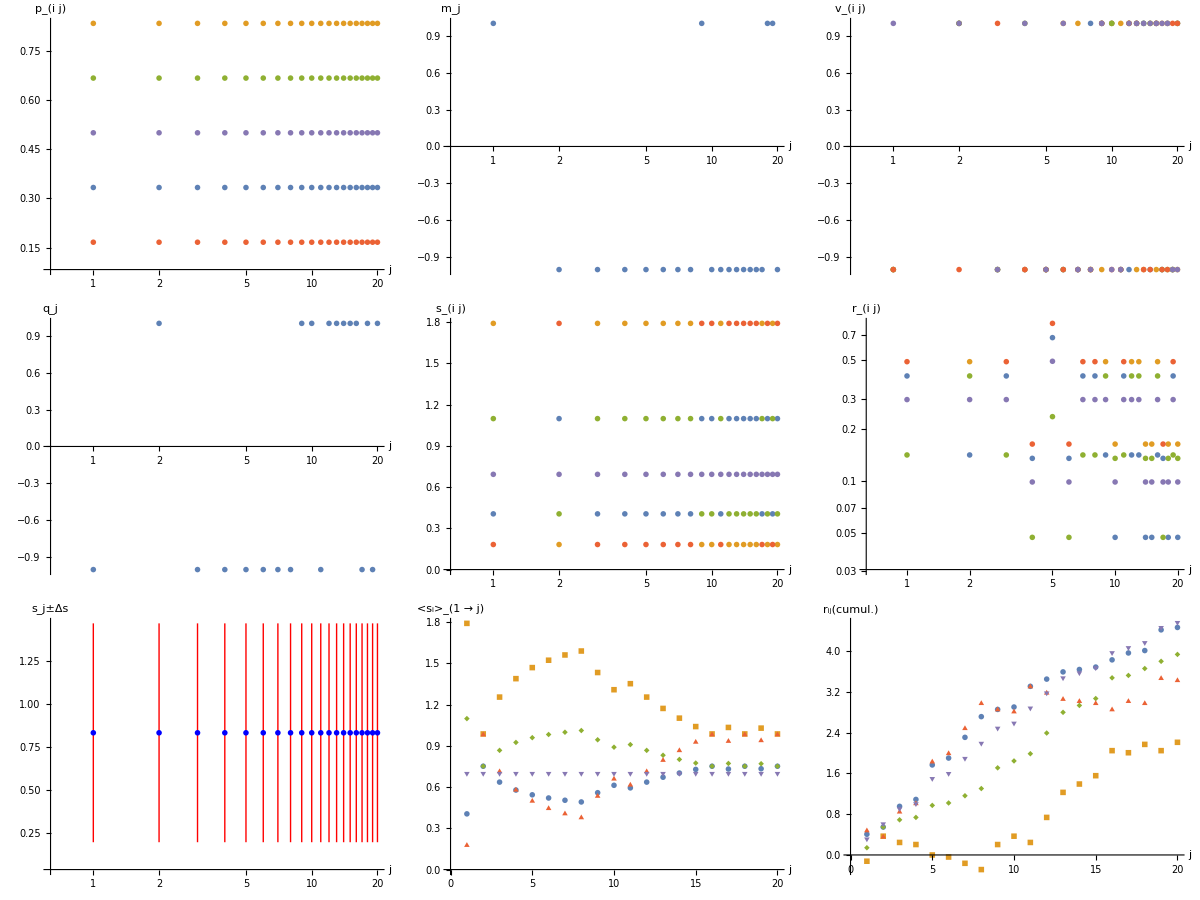

```mathematica
SetUserFunctions[]
RunExperiment[]
ShowPlots[]
```

#### ‘qpredictors’ and ‘nquestions’ can be reinitialized before running another experiment.

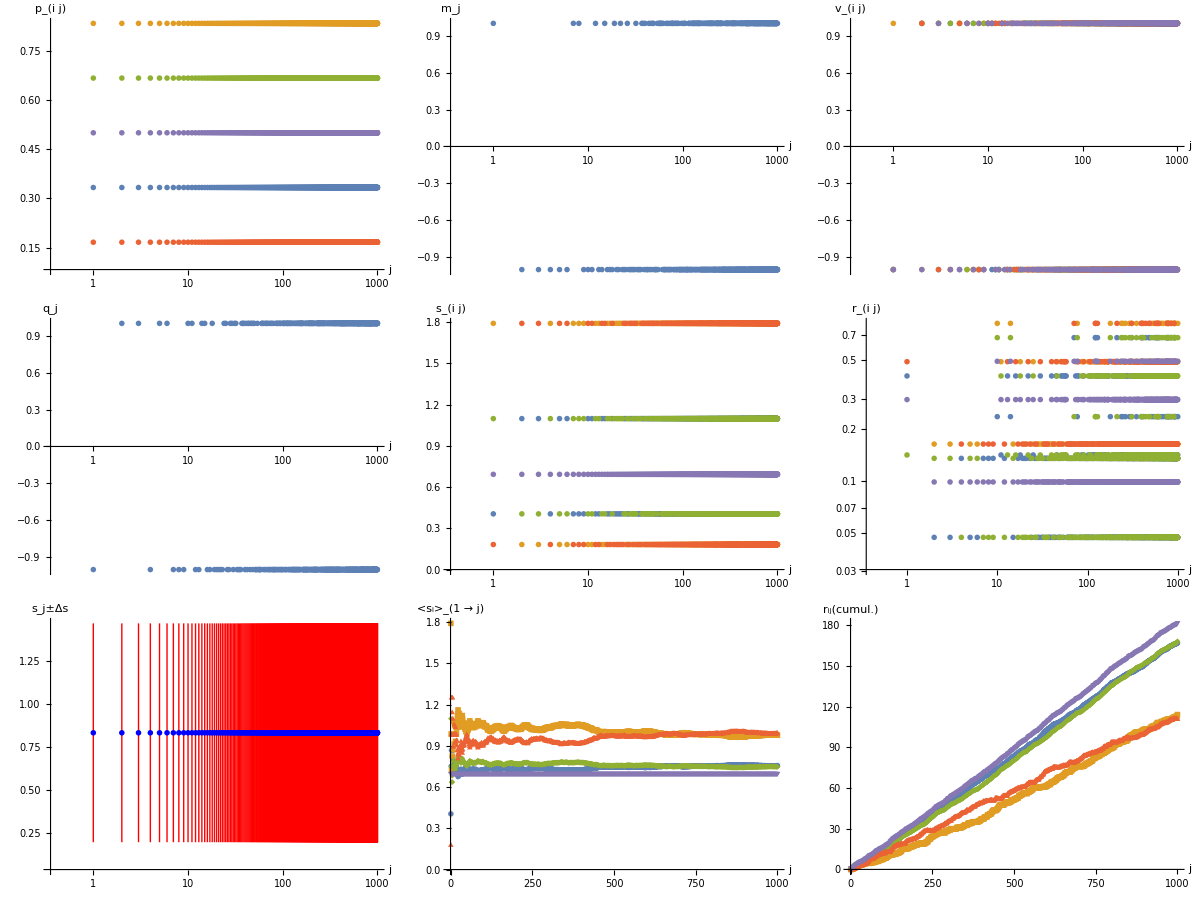

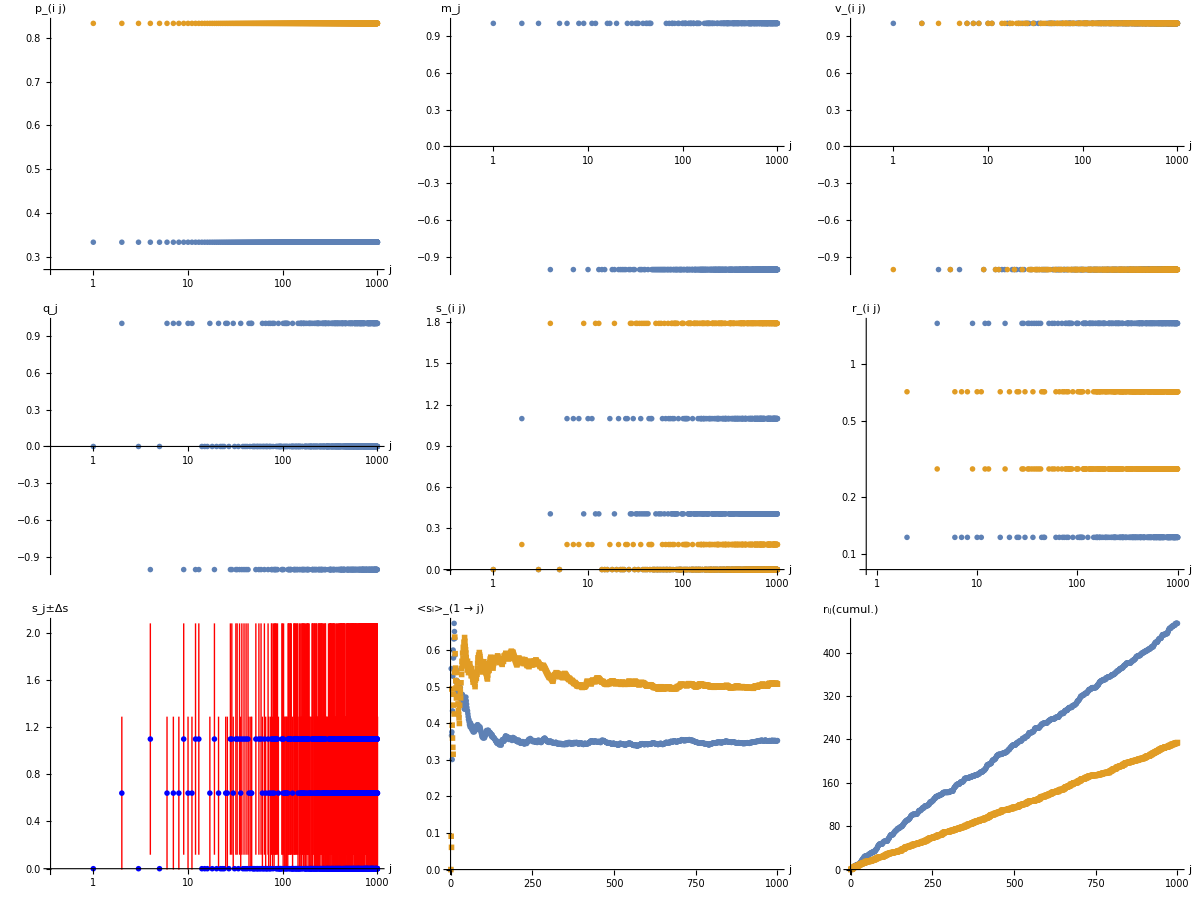

```mathematica
nquestions=1000;
RunExperiment[]
ShowPlots[]

npredictors=2;
RunExperiment[]
ShowPlots[]
```

#### work in progress: cumulative rewards (here for last experiment, with user functions)

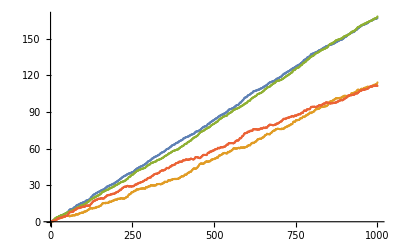

```mathematica
Cumulative[array_]:=Module[
{i,output={array[[1]]},size=array//Length,c},

For[i=2,i≤ size,i++,
c=array[[i]]+output[[i-1]];
AppendTo[output,c];

];
output//N
]
r1=EXPERIMENT[[4,All,6]][[All,1]]//Cumulative;
r2=EXPERIMENT[[4,All,6]][[All,2]]//Cumulative;r3=EXPERIMENT[[4,All,6]][[All,3]]//Cumulative;r4=EXPERIMENT[[4,All,6]][[All,4]]//Cumulative;
ListPlot[{r1,r2,r3,r4}]
```

```mathematica
EXPERIMENT//Length
```

5

```mathematica
RunExperiment[]
```

```mathematica
MakePlots[]
```

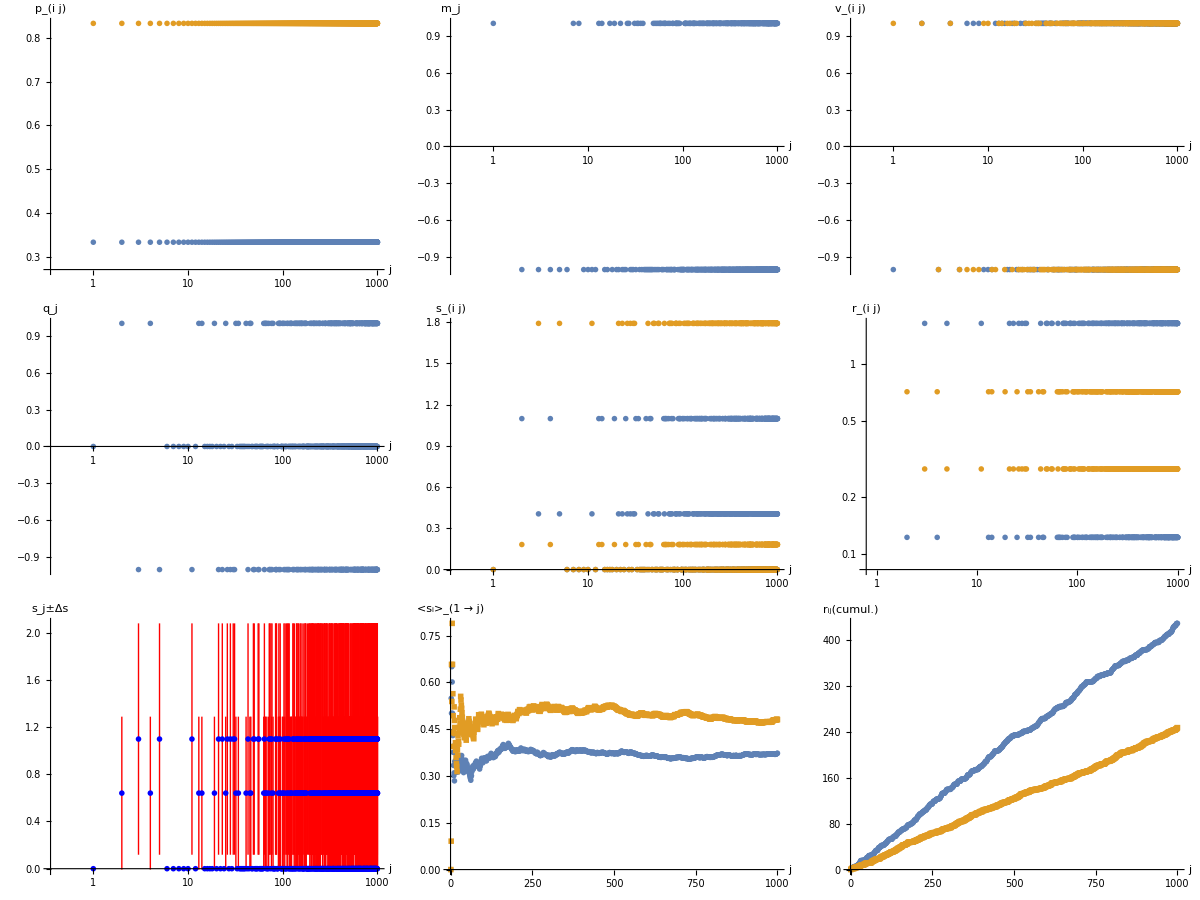

```mathematica
ShowPlots[]
```

```mathematica
npredictorsUSER=4;
$Path=Join[$Path,{NotebookDirectory[]}];
<<EQLab`
```

```mathematica
For[i=1,i≤4,i++,RunExperiment[]];
```